```mathematica
f[x_]=exp(x-(x/4)^2)*th((x/11)^3+1/3);
```

```mathematica
a=0;b=6;n=10;h=(b-a)/n;
```

```mathematica
data=N[Table[{a+i*h,f[a+i*h]},{i,0,n}]];
```

```mathematica
spl1=Interpolation[data,Method->"Spline"]
```

InterpolatingFunction[{{0., 6.}}, <>]

```mathematica
gr1=Plot[f[x],{x,0,6},PlotStyle->Red];
```

```mathematica
gr2=ListPlot[data,PlotStyle->PointSize[0.015]];
```

```mathematica
gr3=Plot[spl1[x],{x,0,6},PlotStyle->Green];
```

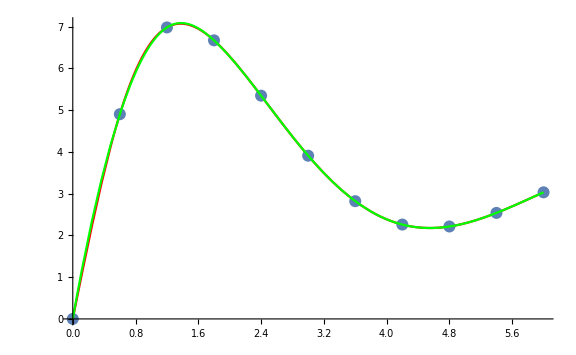

```mathematica
Show[gr1,gr2,gr3,ImageSize->Large]
```

```mathematica
Needs["Splines`"]
```

```mathematica
spl2=SplineFit[data,Cubic]
```

SplineFunction[Cubic, {0.,10.}, <>]

```mathematica
Clear[t];gr4=ParametricPlot[spl2[t],{t,0,6}];
```

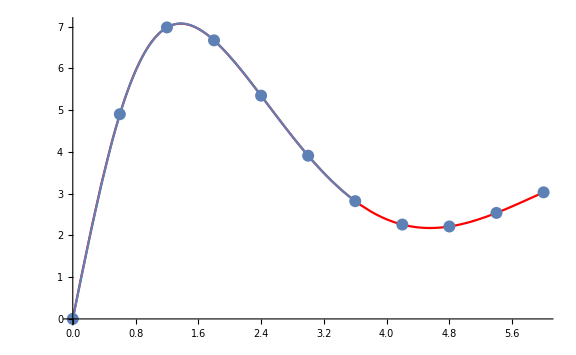

```mathematica
Show[gr1,gr2,gr4,ImageSize->Large]
```

```mathematica
spl1[2.4316]
```

5.27021

```mathematica
spl2[(2.4316-a)/h]
```

{2.4316,5.26999}

```mathematica
f[2.4316]
```

5.26999

```mathematica
S3[2.4316]
```

5.26999

```mathematica
n=Length[data];
```

```mathematica
h=Table[data[[i+1,1]]-data[[i,1]],{i,n-1}];
```

```mathematica
a=Table[data[[i,2]],{i,n}];
```

```mathematica
alpha=Table[3/h[[i]]*(a[[i+1]]-a[[i]])-3/h[[i-1]]*(a[[i]]-a[[i-1]]),{i,2,n-1}];
```

```mathematica
l=Table[0,{i,n}];
```

```mathematica
mu=Table[0,{i,n}];
```

```mathematica
z=Table[0,{i,n}];
```

```mathematica
l[[1]]=1;
```

```mathematica
mu[[1]]=0;
```

```mathematica
z[[1]]=0;
```

```mathematica
For[i=2,i<=n-1,i++,l[[i]]=2*(data[[i+1,1]]-data[[i-1,1]])-h[[i-1]]*mu[[i-1]];
mu[[i]]=h[[i]]/l[[i]];
z[[i]]=(alpha[[i-1]]-h[[i-1]]*z[[i-1]])/l[[i]];]
```

```mathematica
l[[n]]=1;
```

```mathematica
z[[n]]=0;
c=Table[0,{i,n}];
b=Table[0,{i,n-1}];
d=Table[0,{i,n-1}];
```

```mathematica
For[j=n-1,j>=1,j--,c[[j]]=z[[j]]-mu[[j]]*c[[j+1]];
b[[j]]=(a[[j+1]]-a[[j]])/h[[j]]-h[[j]]*(c[[j+1]]+2*c[[j]])/3;
d[[j]]=(c[[j+1]]-c[[j]])/(3*h[[j]]);]
```

```mathematica
S3[x_]:=Module[{j},j=1;
While[x>data[[j+1,1]],j++];
a[[j]]+b[[j]]*(x-data[[j,1]])+c[[j]]*(x-data[[j,1]])^2+d[[j]]*(x-data[[j,1]])^3]
```

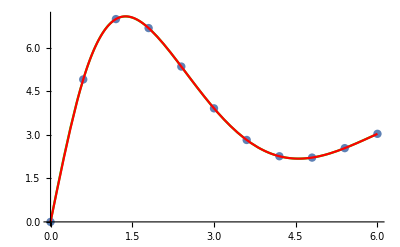

```mathematica
Show[Plot[f[x],{x,0,6}, PlotStyle->Green],ListPlot[data,PlotStyle->PointSize[0.015], PlotStyle->Blue],Plot[S3[x],{x,0,6}, PlotStyle->Red]]
```